```mathematica
(* the groupoid of isomorphisms *)

compose[iso[a_, b_], iso[c_, d_]] := iso[Composition[c, a], Composition[b, d]]

itself := iso[Identity, Identity]

invert[iso[from_, to_]] := iso[to, from]

as[iso[_, toB_], iso[fromA_, _], x_] := toB[fromA[x]]

borrowFrom[iso[fromB_, toB_], f_, iso[fromA_, toA_], x_] := 
 toA[fromB[f[toB[fromA[x]]]]]

borrowFrom2[iso[fromB_, toB_], f_, iso[fromA_, toA_], x_, y_] := 
   toA[fromB[f[toB[fromA[x]], toB[fromA[y]]]]]

(*  sequences to/from multisets *)

list2mset[{}] := {}
list2mset[xs_] := FoldList[Plus, First[xs], Rest[xs]]

mset2list[xs_] := Differences[Prepend[Sort[xs], 0]]

(*  sequences to/from sets *)

list2set[{}] := {}
list2set[xs_] := list2mset[Prepend[Map[succ, Rest[xs]], First[xs]]]

set2list[{}] := {}
set2list[xs_] := Module[
  {ys}, ys = mset2list[xs];
  Prepend[Map[pred, Rest[ys]], First[ys]]]

succ[x_Integer] := x + 1

pred[x_Integer] := x - 1

(* natural numbers to/from sets *)

nat2set[n_Integer] := Module[{bs},
  bs=Reverse[IntegerDigits[n, 2]];
  Pick[Range[0,Length[bs]-1],bs,1]
]

set2nat[xs_] := Fold[Plus, 0, Map[2^# &, xs]]

(* basic encoders populating the groupoid of isomorphisms *)

list := itself

mset := iso[mset2list, list2mset]

set := iso[set2list, list2set]

nat := compose[iso[nat2set, set2nat], set]

(* bitwise pairing/unpairing *)

rebase[n_Integer, oldBase_Integer, newBase_Integer] :=
   FromDigits[IntegerDigits[n, oldBase], newBase]

bPair[{x_, y_}] := rebase[x, 2, 4] + 2*rebase[y, 2, 4]

toBase[b_, n_] := Reverse[IntegerDigits[n, b]]
fromBase[b_, bs_] := FromDigits[Reverse[bs], b]

bUnpair[n_Integer] := Module[{ps, xs, ys},
  ps = Partition[Append[toBase[2, n], 0], 2];
  xs = Map[First, ps]; ys = Map[Last, ps];
  {fromBase[2, xs], fromBase[2, ys]}
  ]
   
nat2 := compose[iso[bPair, bUnpair], nat]

(* cons,uncons derived from this unpairing *)

bCons[{x_,y_}] := succ[bPair[x,y]]
bUncons[z_] := bUnpair[pred[z]]

(* Pepis-Kalmar pairing/unpairing *)

cons[x_, y_] := 2^x (2*y + 1)

hd[z_] := IntegerExponent[z, 2]

tl[z_] := Quotient[Quotient[z, 2^hd[z]] - 1, 2]

pPair[{x_, y_}] := pred[cons[x, y]]

pUnpair[z_] := {hd[succ[z]], tl[succ[z]]}

pnat2 := compose[iso[pPair, pUnpair], nat]


(* k-tuple encodings *)

transposePad[xss_] := Transpose[
  Map[PadRight[#, Max[Map[Length, xss]]] &, xss]
  ]

toTuple[k_, n_] := PadRight[Map[
   fromBase[2, #] &,
   transposePad[Map[toBase[2, #] &, toBase[2^k, n]]]
   ], k]

fromTuple[ns_] := fromBase[
  2^Length[ns],
  Map[fromBase[2, #] &, transposePad[Map[toBase[2, #] &, ns]]]
  ] 

nats[k_] := compose[iso[fromTuple, toTuple[k, #] &], nat]

nat2tlist[0] := {}
nat2tlist[n_] := Apply[toTuple[succ[#1], #2] &, pUnpair[pred[n]]]

tlist2nat[{}] := 0
tlist2nat[ns_] := succ[pPair[{pred[Length[ns]], fromTuple[ns]}]]

tlist := compose[iso[tlist2nat, nat2tlist], nat]

(* Hereditarily finite structures *)

unrank[f_, n_] := Map[unrank[f, #] &, f[n]]

rank[g_, ts_] := g[Map[rank[g, #] &, ts]]

lift[iso[f_, g_]] := iso[rank[g, #] &, unrank[f, #] &]

hff := compose[lift[nat], nat]

natSet := iso[nat2set, set2nat]

hfs := compose[lift[natSet], nat]

natMset := iso[as[mset, nat, #] &, as[nat, mset, #] &]

hfm := compose[lift[natMset], nat]

(* canonical representations as list of unlabeled edges *)

toEdges[_, m_, n_] := {} /; n <= m
toEdges[f_, m_, n_] := Module[{ns, ps, pss},
  ns = f[n];
  ps = Map[n -> # &, ns];
  pss = Map[toEdges[f, m, #] &, ns];
  Apply[Union, Prepend[pss, ps]]
  ]

(* canonical representations as list of labeled edges *)

toOrdEdges[_, m_, n_] := {} /; n <= m
toOrdEdges[f_, m_, n_] := Module[{ns, ps, pss},
  ns = f[n];
  ps = MapIndexed[{n -> #1, First[#2] - 1} &, ns];
  pss = Map[toOrdEdges[f, m, #] &, ns];
  Apply[Union, Prepend[pss, ps]]
  ]

nat2list[n_] := as[list, nat, n]

nat2mset[n_] := as[mset, nat, n]

(* encodings of digraphs, DAGs hypergraphs  
  parameterized by pairing/unpairing functions 
*)

pair := bPair 
unpair := bUnpair

toEdge[{x_, y_}] := x -> y

fromEdge[x_ -> y_] := {x, y}

(* edge encodings *)

ordUnpair[z_] := toEdge[unpair[z]]
ordPair[xy_] := pair[fromEdge[xy]]

unordUnpair[z_] := toEdge[as[mset, list, unpair[z]]] 
unordPair[xy_] := pair[as[list, mset, fromEdge[xy]]]

upwardUnpair[z_] := toEdge[as[set, list, unpair[z]]] 
upwardPair[xy_] := pair[as[list, set, fromEdge[xy]]]

(* digraphs *)
set2digraph[xs_] := Map[ordUnpair, xs]
digraph2set[ps_] := Map[ordPair, ps]

digraph := compose[iso[digraph2set, set2digraph], set]

(* graphs *)
set2graph[xs_] := Map[unordUnpair, xs]
graph2set[ps_] := Map[unordPair, ps]

graph := compose[iso[graph2set, set2graph], set]

(* DAGs *)

set2dag[xs_] := Map[upwardUnpair, xs]
dag2set[ps_] := Map[upwardPair, ps]

dag := compose[iso[dag2set, set2dag], set]

(* set systems (hypergraphs) *)

hgraph2set[xss_] := Map[Composition[pred, set2nat], xss]

set2hgraph[xs_] := Map[Composition[nat2set, succ], xs]

hgraph := compose[iso[hgraph2set, set2hgraph], set]

(* binaray relations as (sparse) 0/1 matrices *)

toEdge1[{x_, y_}->_] := pred[x] -> pred[y]
fromEdge1[x_ -> y_] := {succ[x], succ[y]}->1
plainArrayRules[a_]:= Most[ArrayRules[a]]

toVertices[es_]:=Apply[Union,Map[fromEdge,es]]

digraph2binrel[{}]:=SparseArray[{{0}},{1,1}]
digraph2binrel[es_] := Module[{l},
  l=1+Max[toVertices[es]];
  SparseArray[Map[fromEdge1,es],{l,l}
]]

binrel2digraph[r_] := Map[toEdge1,plainArrayRules[r]]

binrel := compose[iso[binrel2digraph, digraph2binrel], digraph]

(* matrix encoders *)
nat2xmat[n_] := Module[{dds,d,ds,c,dims},
  {dds,c}=pUnpair[n];
  {d,ds}=pUnpair[dds];
  dims=Map[succ,toTuple[succ[d],ds]];
  nat2dmat[dims->c]
]

nat2dmat[dims_->n_]:= Module[{l,ns,m},
  l=Apply[Times,dims];
  ns=toTuple[l,n];
  {m}=rpartition[dims,ns];
  m
]

rpartition[{},xs_]:= xs
rpartition[ds_,xs_] := Partition[rpartition[Rest[ds],xs],First[ds]]

dmat2nat[m_] := Dimensions[m]->fromTuple[Flatten[m]]

dmat[dims_] := compose[iso[Last[dmat2nat[#]]&, nat2dmat[dims->#]&], nat]
  
(* visualization *)

plotDigraph[edges_] := LayeredGraphPlot[
  edges, VertexLabeling -> True, DirectedEdges -> True]

plotGraph[edges_] := GraphPlot[
  edges, VertexLabeling -> True,  DirectedEdges -> False]

plotDig[n_] := plotDigraph[as[digraph, nat, n]]
plotDag[n_] := plotDigraph[as[dag, nat, n]]
plotG[n_] := plotGraph[as[graph, nat, n]]

plotHSet[f_, m_, n_] := plotDigraph[toEdges[f, m, n]]

showHFS[n_] := plotHSet[nat2set, 0, n]

plotHlist[f_, m_, n_] := plotDigraph[toOrdEdges[f, m, n]]

showHFF[n_] := plotHlist[nat2list, 0, n]
showTHFF[n_] := plotHlist[nat2tlist, 0, n]

showHFM[n_] := plotHlist[nat2mset, 0, n]

showBPairs[n_] := plotHlist[bUnpair, 1, n]
showCPairs[n_] := plotHlist[bUncons, 0, n]

showPPairs[n_] := plotHlist[pUnpair, 1, n]

showTuples[k_, n_] := plotHlist[toTuple[k, #] &, 1, n]

pplot[f_, m_] := ListLinePlot[Map[f, Range[0, m]]]

pplotB[m_] := pplot[bUnpair, m]
pplotP[m_] := pplot[pUnpair, m]

toMatrix[f_, m1_, m2_] := Module[
  {ns, xys, zs}, ns = Range[m1, m2];
  xys = Tuples[ns, 2];
  zs = Map[f, xys];
   MapThread[Append, {xys, zs}]]

plot3d[f_, m1_, m2_] := ListPlot3D[
  toMatrix[f, m1, m2], Mesh -> None, ColorFunction -> Hue]

pplot3D[f_, m_] := plot3d[f, 0, m+4]

pplot3Db[m_] := pplot3D[bPair, m]
pplot3Dp[m_] := pplot3D[pPair, m]

aplot[m_]:= ArrayPlot[m,Mesh->True,ColorRules->{1->Red,0->Black}]

binrelPlot[n_]:= aplot[Normal[as[binrel,nat,n]]]

(* interactive visualization *)
manipulateAS[label_,dataType_, m_] := Manipulate[
  as[dataType, nat, x], {x, 0, 2^m - 1, 1},
  Frame->True,
  FrameLabel->label
  ]

manipulateFig[f_, m_] := Manipulate[
  f[x], {x, 0, 2^m - 1, 1},
  Frame->True,
  FrameLabel->f
]

manipulateT[k_, m_] := Manipulate[showTuples[
   tupleSize, n], {tupleSize, 2, k, 1}, {n, 2, 2^m - 1, 1}]

manipulateT3[m_] := Manipulate[ListSurfacePlot3D[
   Map[toTuple[3, #] &, Range[1, n]],
   Mesh -> None], {n, 2^4, 2^(m+4), 1}
  ]

manipulateAsSet[m_] := manipulateAS["as set",set, m]
manipulateAsMset[m_] := manipulateAS["as multiset",mset, m]
manipulateAsList[m_] := manipulateAS["as list",list, m]
manipulateAsHFS[m_] := manipulateAS["as HFS",hfs, m]
manipulateAsHFM[m_] := manipulateAS["as HFM",hfm, m]
manipulateAsHFF[m_] := manipulateAS["as HFF",hff, m]

manipulateAsBP[m_] := manipulateAS["as bitwise pair",nat2, m]
manipulateAsPP[m_] := manipulateAS["as Pepis pair",pnat2, m]
manipulateAsDig[m_] := manipulateAS["as digraph",digraph, m]
manipulateAsDag[m_] := manipulateAS["as DAG",dag, m]
manipulateAsG[m_] := manipulateAS["as undirected graph",graph, m]
manipulateAsH[m_] := manipulateAS["as hypergraph",hgraph, m]

manipulateHFF[m_] := manipulateFig[showHFF, m]
manipulateHFM[m_] := manipulateFig[showHFM, m]
manipulateHFS[m_] := manipulateFig[showHFS, m]

manipulateBPairs[m_] := manipulateFig[showBPairs, m]
manipulateCPairs[m_] := manipulateFig[showCPairs, m]

manipulatePPairs[m_] := manipulateFig[showPPairs, m]
manipulateTuples[k_, m_] := manipulateT[k,m]
manipulateTriplets[m_] := manipulateT3[m]
manipulateTHFF[m_] := manipulateFig[showTHFF, m]

manipulateplotB[m_] := manipulateFig[pplotB, m]
manipulateplotP[m_] := manipulateFig[pplotP, m]
manipulateB3d[m_] := manipulateFig[pplot3Db, m]
manipulateP3d[m_] := manipulateFig[pplot3Dp, m]
manipulateDig[m_] := manipulateFig[plotDig, m]
manipulateDag[m_] := manipulateFig[plotDag, m]
manipulateG[m_] := manipulateFig[plotG, m]

toSound[f_,n_]:=Sound[Map[SoundNote[#,1,"Cello"]&,f[n]]]

manipulateAsSound[f_,m_]:=Manipulate[toSound[nat2list[#]&,x],{x,0,2^m-1,1}]

manipulateBinrelMat[m_]:= Manipulate[MatrixForm[as[binrel,nat,x]],{x,1,2^m-1,1}]
manipulateBinrelPlot[m_]:= Manipulate[binrelPlot[x],{x,1,2^m-1,1}]
```

```mathematica
manipulateAsMset[16]
```

```mathematica
manipulateAsList[16]
```

```mathematica
manipulateAsSound[nat2list,18]
```

```mathematica
manipulateAsHFS[16]
```

```mathematica
manipulateAsHFM[16]
```

```mathematica
manipulateAsHFF[16]
```

```mathematica
manipulateAsBP[16]
```

```mathematica
manipulateAsPP[16]
```

```mathematica
manipulateAsDig[16]
```

```mathematica
manipulateAsDag[16]
```

```mathematica
manipulateAsG[16]
```

```mathematica
manipulateAsH[16]
```

```mathematica
manipulateHFF[16]
```

```mathematica
manipulateHFM[16]
```

```mathematica
manipulateHFS[16]
```

```mathematica
manipulateBPairs[16]
```

```mathematica
manipulateCPairs[16]
```

```mathematica
manipulatePPairs[16]
```

```mathematica
manipulateplotB[10]
```

```mathematica
manipulateplotP[10]
```

```mathematica
manipulateB3d[6]
```

```mathematica
manipulateP3d[6]
```

```mathematica
manipulateTuples[8,16]
```

```mathematica
manipulateTriplets[4]
```

```mathematica
manipulateTHFF[16]
```

```mathematica
manipulateDig[16]
```

```mathematica
manipulateDag[16]
```

```mathematica
manipulateG[16]
```

```mathematica
manipulateBinrelMat[31]
```

```mathematica
manipulateBinrelPlot[31]
```

```mathematica
Manipulate[MatrixForm[nat2dmat[{8,8}->3^xx]],{x,0,2^8-1,1}]
```

```mathematica
Manipulate[MatrixForm[nat2dmat[{8,8}->3^x]],{x,0,2^8-1,1}]
```

{{1,3},{1,4},{1,2},{3,2},{3,4}}

{{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}}

{{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6},{4,5},{4,6},{5,6}}

{{3,1},{3,2},{4,1},{4,2},{5,2},{5,4},{1,3},{2,3},{1,4},{2,4},{2,5},{4,5}}

13

1

{1,1,3,16,218,9608,1540944,882033440,1793359192848,13027956824399552,341260431952972580352}

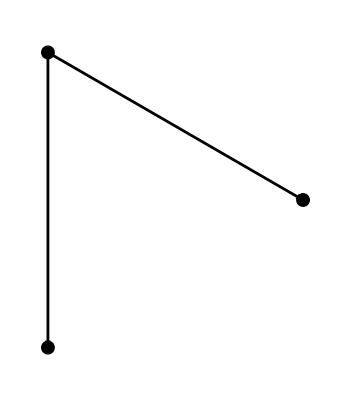
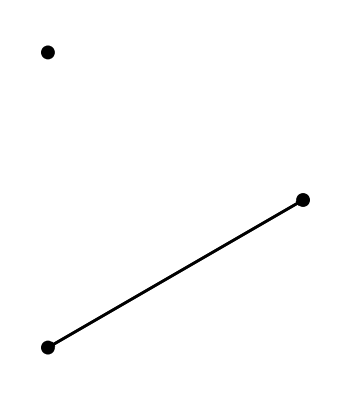
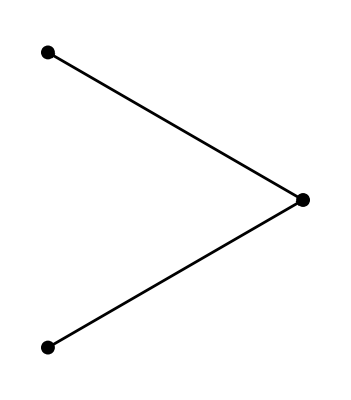
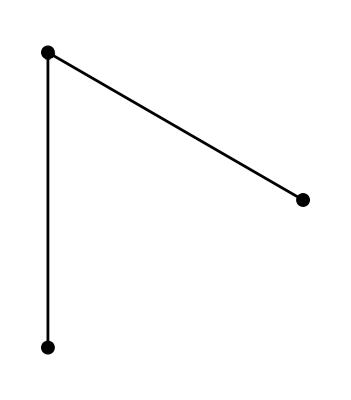

```mathematica
Needs["GraphUtilities`"];
Needs["Combinatorica`"];
ToOrderedPairs[FromOrderedPairs[{{1,3}, {1,4}, {1,2},{3,2}, {3,4}}]]
ToOrderedPairs[MakeGraph[Range[0,5],#1<#2&]]
ToOrderedPairs[MakeGraph[Range[0,5],#1<#2&]]
ToOrderedPairs[RandomGraph[5,0.5]]
(*ShowGraph[MakeGraph[Range[1,16],Divisible[#1,#2]&],VertexLabel->True]*)
(*ShowGraph[DeBruijnGraph[{a,b,c},3]]*)
(*ShowGraph[MakeGraph[Range[1,16],Divisible[#1,#2]&],VertexLabel->True]*)
NumberOfDirectedGraphs[4,3]
NumberOfDirectedGraphs[2,2]
Map[NumberOfDirectedGraphs,Range[0,10]]
Map[ShowGraph,ListGraphs[3,2,Directed]]
```

```mathematica
{{1,3},{1,4},{1,2},{3,2},{3,4}}
```

{{1,3},{1,4},{1,2},{3,2},{3,4}}

```mathematica
(*ShowGraph[RandomGraph[5,0.5]]*)
```

```mathematica
Map[Plus[1,#]&,{2,3,4}]
```

{3,4,5}

```mathematica
unrank[nat2set,42]
```

{{{}},{{},{{}}},{{},{{{}}}}}

```mathematica
rank[set2nat,{{{}},{{},{{}}},{{},{{{}}}}}]
```

42

```mathematica
as[hfm,nat,42]
```

{{{}},{{{}}},{{},{}}}

```mathematica
as[hff,nat,2009]
```

{{},{{{}}},{},{{}},{},{},{},{}}

```mathematica
unrank[nat2set,42]
```

{{{}},{{},{{}}},{{},{{{}}}}}

```mathematica
hfs
```

iso[Composition[set2list,nat2set,rank[set2nat,#1]&],Composition[unrank[nat2set,#1]&,set2nat,list2set]]

```mathematica
nat2list[42]
```

{1,1,1}

```mathematica
as[pnat2,nat,2009]
```

{1,502}

```mathematica
borrowFrom2[nat,Plus,set,{1,2,4,9}, {2,3,6,7}]
```

{1,5,6,7,9}

```mathematica
Map[Composition[bPair,bUnpair],Range[0,10]]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
pPair[0,0]
```

pPair[0,0]

```mathematica
pPair[0,0]
```

pPair[0,0]

```mathematica
as[set,nat,2009]
```

{0,3,4,6,7,8,9,10}

```mathematica
as[set,list,{0,0,0,0,1}]
```

{0,1,2,3,5}

```mathematica
set2list[{0,1,2,3}]
```

{0,0,0,0}

```mathematica
nat2set[set2nat[{2,5,8}]]
```

{2,5,8}

```mathematica
nat2set[set2nat[{a,b,c}]]
```

nat2set[2^a+2^b+2^c]

```mathematica
list2set[{a,b,c, d}]
```

{a,a+succ[b],a+succ[b]+succ[c],a+succ[b]+succ[c]+succ[d]}

```mathematica
set2list[list2set[{3,0,0,1,3,2,0,1,1}]]
```

{3,0,0,1,3,2,0,1,1}

```mathematica
list2mset[mset2list[{3,0,1,0,0,5}]]
```

{0,0,0,1,3,5}

```mathematica
inflate[2009]
```

inflate[2009]

```mathematica
parity[8]
```

parity[8]

```mathematica
deflate' [2008]
```

deflate'[2008]

```mathematica
bPair [22,37]
```

bPair[22,37]

```mathematica
bPair[22,37]
```

bPair[22,37]

```mathematica
2358
bUnpair[2358]
```

2358

{22,37}

```mathematica
bUnpair[2009]
```

{61,26}

```mathematica
rebase[2009,2,4]
```

1397057

```mathematica
list2mset[{0,1,1,1,2}]
```

{0,1,2,3,5}

```mathematica
Riffle[{1,2,3,4},{50,60}]
```

{1,50,2,60,3,50,4}

```mathematica
{1,50,2,60,3,50,4}

PadRight[{1,2,3},10]
```

{1,50,2,60,3,50,4}

{1,2,3,0,0,0,0,0,0,0}

```mathematica
pair[{2,3}]
```

14

```mathematica
(*ShowGraph[FromOrderedPairs[Map[fromEdge,as[dag,nat,2009]]]]*)
```

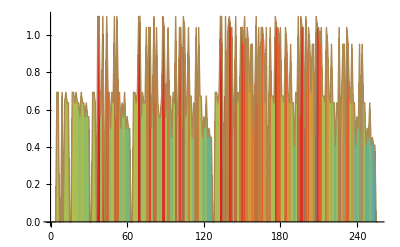

```mathematica
ListLinePlot[Map[N[Entropy[as[list,nat,#], ]]&,Range[1,2^8]],Filling->Axis,ColorFunction->"Rainbow"]
```

```mathematica
leftXor[n_]:= BitXor[n,BitShiftLeft[n,1]]
leftAnd[n_]:= BitAnd[n,BitShiftLeft[n,1]]

xors[m_] := Map[leftXor,Range[0,2^m-1]]
ands[m_] := Map[leftAnd,Range[0,2^m-1]]

both[m_] := Map[succ,MapThread[Plus,{xors[m],ands[m]}]]

powset[0] := 1
powset[n_] :=leftXor[powset[pred[n]]]

x3[m_] := Map[3*#+1&,Range[0,2^m-1]]

p1[m_]:= ListLinePlot[{
x3[m],
xors[m],
ands[m]}]

p2[m_]:=ListLinePlot[{x3[m],both[m]}]

p3[n_]:=ListLinePlot[{Map[powset,Range[0,n]]}]
```

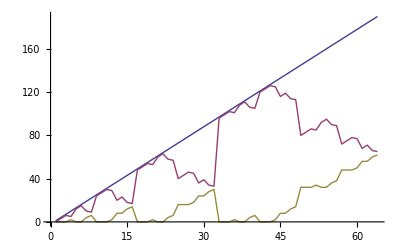

```mathematica
p1[17]
```

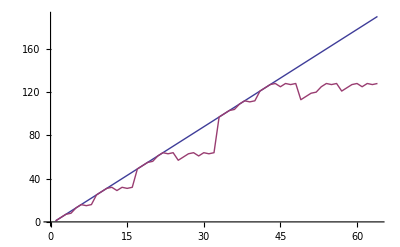

```mathematica
p2[6]
```

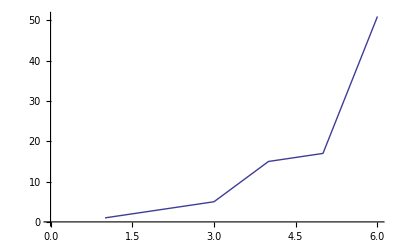

```mathematica
p3[5]
```

```mathematica
xors[5]
```

{0,3,6,5,12,15,10,9,24,27,30,29,20,23,18,17,48,51,54,53,60,63,58,57,40,43,46,45,36,39,34,33}

```mathematica
ands[5]
```

{0,0,0,2,0,0,4,6,0,0,0,2,8,8,12,14,0,0,0,2,0,0,4,6,16,16,16,18,24,24,28,30}

```mathematica
both[5]
```

{0,3,6,7,12,15,14,15,24,27,30,31,28,31,30,31,48,51,54,55,60,63,62,63,56,59,62,63,60,63,62,63}

```mathematica
x3[5]
```

{1,4,7,10,13,16,19,22,25,28,31,34,37,40,43,46,49,52,55,58,61,64,67,70,73,76,79,82,85,88,91,94}

```mathematica
leftXor[127]
```

129

```mathematica
leftAnd[127]
```

126

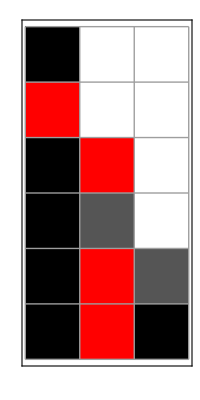

```mathematica
ArrayPlot[as[hgraph,nat,1111],Mesh->True,Frame->True,ColorRules->{1->Red,0->Black}]
```

{0→0,1→0,1→1,2→0,3→0,2→1}

{{1,0,0,0},{1,1,0,0},{1,1,0,0},{1,0,0,0}}

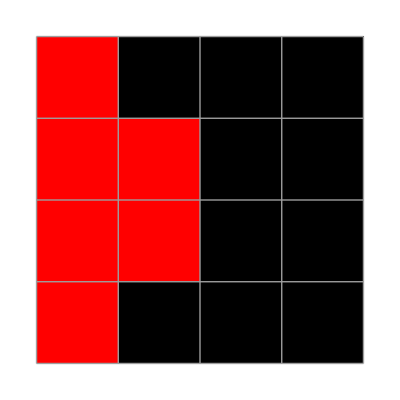

```mathematica
as[digraph,nat,123] (*[[1,0,0,0],[1,1,0,0],[1,1,0,0],[1,0,0,0]]*)
Normal[digraph2binrel[as[digraph,nat,123]]]
ArrayPlot[Normal[digraph2binrel[as[digraph,nat,123]]],Mesh->True,ColorRules->{1->Red,0->Black}]
```